```mathematica
datapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Isolated_Measurements_230202\\";
datapathFolders = FileNames["*",datapath];
importdata = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",datapathFolders[[board]]]),{board,1,Dimensions[datapathFolders][[1]]}];

datapathImpedances = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Impedances_Isolated_Cells_230202\\";
importedImpedances = Import[#,"Table"]&/@(FileNames[datapathImpedances<>"*.txt"]);
```

```mathematica
importdata//Dimensions
```

{9}

```mathematica
nodes = {{7,1},{6,2},{1,4},{2,4},{4,4},{5,4},{7,4},{8,4},{4,5},{4,6},{4,7},{7,8}};
consideration = {2,4,5,6,7,9,10,11};
consideredNodes = nodes[[consideration]];
reordering = {};
shuntR = 10.853;

voltageDataImpedances = Table[importedImpedances[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importedImpedances][[1]]},{entry,1,4}];

voltageDataOrdered = Table[importdata[[board,j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata[[board]]][[1]]},{entry,1,2}];

frequencyArray = voltageDataOrdered[[1,1,1,;;,1]];

ticks = Table[{(Dimensions[frequencyArray][[1]])*i,ToString[i]},{i,1,5}];
```

```mathematica
impedancesIsolated = Table[{frequencyArray[[freq]],(shuntR*(voltageDataImpedances[[j,3,freq,2]])*Exp[I(voltageDataImpedances[[j,4,freq,2]])*2π/360])/(((voltageDataImpedances[[j,1,freq,2]])*Exp[I(voltageDataImpedances[[j,2,freq,2]])*2π/360])-((voltageDataImpedances[[j,3,freq,2]])*Exp[I(voltageDataImpedances[[j,4,freq,2]])*2π/360]))},{j,1,Dimensions[importedImpedances][[1]]},{freq,1,Length[frequencyArray]}];

impedancesIsolatedPlots = Table[ListLinePlot[Abs[impedancesIsolated[[2*(j-1)+sub]]],PlotLabel->"Node: "<>ToString[nodes[[j]]]<>" Sublattice "<>ToString[If[sub==1,"A","B"]],PlotRange->All,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Ticks->{ticks,Automatic},PlotLegends->{"Amplitude of impedance spectrum of isolated cells"}],{j,1,Dimensions[importedImpedances][[1]]/2},{sub,1,2}];

impedancesIsolatedPlotsZoomed = Table[ListLinePlot[Abs[impedancesIsolated[[2*(j-1)+sub]]],PlotLabel->"Node: "<>ToString[nodes[[j]]]<>" Sublattice "<>ToString[If[sub==1,"A","B"]],PlotRange->{{1800,3200},{0,Max[Abs[impedancesIsolated[[2*(j-1)+sub,200;;550,2]]]]}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Ticks->{ticks,Automatic},PlotLegends->{"Amplitude of impedance spectrum of isolated cells"}],{j,1,Dimensions[importedImpedances][[1]]/2},{sub,1,2}];
```

```mathematica
Manipulate[impedancesIsolatedPlots[[node,sub]],{node,1,Dimensions[importedImpedances][[1]]/2,1},{sub,1,2,1}]
```

```mathematica
mean = Table[Mean[Abs[impedancesIsolated[[2*consideration-1+sub,;;,2]]]],{sub,1,2}];
std = Table[Mean[StandardDeviation[impedancesIsolated[[2*consideration-1+sub,;;,2]]]],{sub,1,2}];
```

```mathematica
impedancesIsolated//Dimensions
consideration
2*consideration-1
```

{24,1000,2}

{2,4,5,6,7,9,10,11}

{3,7,9,11,13,17,19,21}

```mathematica
mean//Dimensions
```

{2,1000}

```mathematica
limitedPlotrange = {{1800,3200},{0,Max[voltageDataOrdered[[board,Which[Dimensions[importdata[[board]]][[1]]==2,
Which[inputSub==outputSub,Which[inputSub==1,1,inputSub==2,2],True,inputSub],
True,
2*(inputSub-1)+outputSub],absarg,200;;550,2]]]}};
```

Part::pkspec1: The expression board cannot be used as a part specification.

```mathematica
voltageDataOrdered//Dimensions
voltageDataOrdered[1]//Dimensions
```

{1,6,2,1000,2}

{1}

```mathematica
configNames = Table[FileNameTake[FileNames[datapath<>"*"][[config]]],{config,1,Dimensions[datapathFolders][[1]]}];

voltagePlots = Table[ListLinePlot[voltageDataOrdered[[board,Which[Dimensions[importdata[[board]]][[1]]==2,
Which[inputSub==outputSub,Which[inputSub==1,1,inputSub==2,2],True,inputSub],
True,
2*(inputSub-1)+outputSub],absarg]],
AxesLabel->{"Frequency [MHz]",If[absarg==1,"Voltage [V]","Phase [Rad]"]},PlotRange->All,PlotLabel->ToString[configNames[[board]]],ImageSize->Large,Ticks->{ticks,Automatic}]
,{board,1,Dimensions[importdata][[1]]},{absarg,1,2},{inputSub,1,2},{outputSub,1,2}];
```

```mathematica
Manipulate[voltagePlots[[meas,absarg,inputSub,outputSub]],{meas,1,Dimensions[importdata][[1]],1},{absarg,1,2,1},{inputSub,1,2,1},{outputSub,1,2,1},SaveDefinitions->True]
```

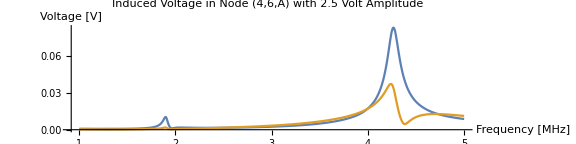

```mathematica
ListLinePlot[{
voltageDataOrdered[[4,2*(1-1)+1,1]],

voltageDataOrdered[[4,2*(2-1)+1,1]]
},
AxesLabel->{"Frequency [MHz]","Voltage [V]"},PlotRange->All,
PlotLabel->"Induced Voltage in Node (4,6,A) with 2.5 Volt Amplitude"
,ImageSize->Large,Ticks->{ticks,Automatic},AspectRatio->1/4,PlotLegends->{"Input Node (4,5,A)","Input Node (4,5,B)"}]
```

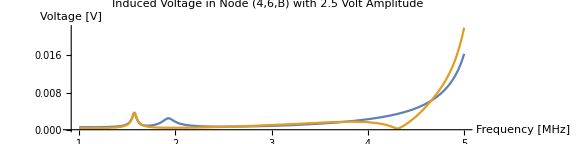

```mathematica
ListLinePlot[{
voltageDataOrdered[[4,2*(1-1)+2,1]],

voltageDataOrdered[[4,2*(2-1)+2,1]]
},
AxesLabel->{"Frequency [MHz]","Voltage [V]"},PlotRange->All,
PlotLabel->"Induced Voltage in Node (4,6,B) with 2.5 Volt Amplitude"
,ImageSize->Large,Ticks->{ticks,Automatic},AspectRatio->1/4,PlotLegends->{"Input Node (4,5,A)","Input Node (4,5,B)"}]
```

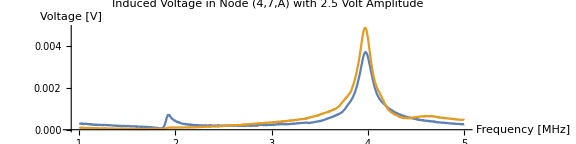

```mathematica
ListLinePlot[{
voltageDataOrdered[[5,2*(1-1)+1,1]],

voltageDataOrdered[[5,2*(2-1)+1,1]]
},
AxesLabel->{"Frequency [MHz]","Voltage [V]"},PlotRange->All,
PlotLabel->"Induced Voltage in Node (4,7,A) with 2.5 Volt Amplitude"
,ImageSize->Large,Ticks->{ticks,Automatic},AspectRatio->1/4,PlotLegends->{"Input Node (4,5,A)","Input Node (4,5,B)"}]
```

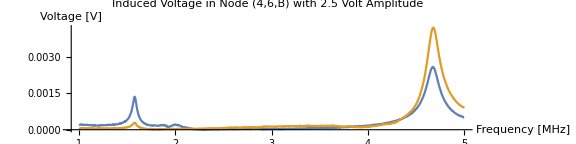

```mathematica
ListLinePlot[{
voltageDataOrdered[[5,2*(1-1)+2,1]],

voltageDataOrdered[[5,2*(2-1)+2,1]]
},
AxesLabel->{"Frequency [MHz]","Voltage [V]"},PlotRange->All,
PlotLabel->"Induced Voltage in Node (4,6,B) with 2.5 Volt Amplitude"
,ImageSize->Large,Ticks->{ticks,Automatic},AspectRatio->1/4,PlotLegends->{"Input Node (4,5,A)","Input Node (4,5,B)"}]
```